```mathematica
Quit[]
```

#### Constants and initial conditions

```mathematica
inix =318400 Kilometers/.Kilometers-> am/384400/.am->1;
iniy =0;
inivx = -1.05 Kilometers/Seconds/.Kilometers-> am/384400/.Seconds-> day/(24*60*60)/.am->1/.day->1;
inivy=0.18 Kilometers/Seconds/.Kilometers-> am/384400/.Seconds-> day/(24*60*60)/.am->1/.day->1;
μe=398600.4418 Kilometers^3/Seconds^2/.Kilometers-> am/384400/.Seconds-> day/(24*60*60)/.am->1/.day->1;
μ=μe;
```

#### Kepler’s equation and derivatives dE/dα

```mathematica
kepler[α_]:=(√μ)/a[α]^(3/2) (t-t0) -eh[α]-(r0[α]/a[α]-1)Sin[eh[α]]-σ0[α]/(√a[α])(1-Cos[eh[α]])
dkepler[α_]:=Evaluate[Collect[kepler'[α],{r0'[α],a'[α],σ0'[α],eh'[α]}]]
dkepler[α];
dehdα=Collect[Solve[dkepler[α]==0,eh'[α]][[1,1,2]],{r0'[α],a'[α],σ0'[α],eh'[α]}];
dehdα
functionrepl[v_]:={
a'[α]->D[a[x0,y0,vx0,vy0],v],
σ0'[α]->D[σ0[x0,y0,vx0,vy0],v],
r0'[α]->D[r0[x0,y0],v],
a[α]->a[x0,y0,vx0,vy0],
σ0[α]->σ0[x0,y0,vx0,vy0],
r0[α]->r0[x0,y0],
eh[α]->eh[x0,y0,vx0,vy0,t,t0]}
dehdx0=dehdα/.functionrepl[x0];
dehdy0=dehdα/.functionrepl[y0];
dehdvx0=dehdα/.functionrepl[vx0];
dehdvy0=dehdα/.functionrepl[vy0];
dehrepl={
D[eh[x0,y0,vx0,vy0,t,t0],x0]->dehdx0,
D[eh[x0,y0,vx0,vy0,t,t0],y0]->dehdy0,
D[eh[x0,y0,vx0,vy0,t,t0],vx0]->dehdvx0,
D[eh[x0,y0,vx0,vy0,t,t0],vy0]->dehdvy0
};
```

-(1. (-(0.34332 (t-1. t0))/a[α]^(5/2)+(r0[α] Sin[eh[α]])/a[α]^2+(0.5 (1.-1. Cos[eh[α]]) σ0[α])/a[α]^(3/2)) a'[α])/(-1.-1. Cos[eh[α]] (-1.+r0[α]/a[α])-(1. Sin[eh[α]] σ0[α])/(√a[α]))+(1. Sin[eh[α]] r0'[α])/(a[α] (-1.-1. Cos[eh[α]] (-1.+r0[α]/a[α])-(1. Sin[eh[α]] σ0[α])/(√a[α])))+(1. (1.-1. Cos[eh[α]]) σ0'[α])/(√a[α] (-1.-1. Cos[eh[α]] (-1.+r0[α]/a[α])-(1. Sin[eh[α]] σ0[α])/(√a[α])))

#### Main function definitions

```mathematica
αs={x0,y0,vx0,vy0};
fs={x,y,vx,vy};
r0[x0_,y0_]:= Sqrt[x0^2+y0^2]
v0[vx0_,vy0_]:= Sqrt[vx0^2+vy0^2]
σ0[x0_,y0_,vx0_,vy0_] := (x0 vx0+y0 vy0)/(√μ)
a[x0_,y0_,vx0_,vy0_]:= (2/r0[x0,y0]-v0[vx0,vy0]^2/μ)^-1
h[x0_,y0_,vx0_,vy0_] := Cross[{x0,y0,0},{vx0,vy0,0}]
ecc[x0_,y0_,vx0_,vy0_]:= Norm[1/μ Cross[{vx0,vy0,0},h[x0,y0,vx0,vy0]] - {x0,y0,0}/r0[x0,y0]]
r[x0_,y0_,vx0_,vy0_,t_,t0_]:=a[x0,y0,vx0,vy0]+(r0[x0,y0]-a[x0,y0,vx0,vy0])Cos[eh[x0,y0,vx0,vy0,t,t0]]+√a[x0,y0,vx0,vy0] σ0[x0,y0,vx0,vy0]Sin[eh[x0,y0,vx0,vy0,t,t0]]
```

```mathematica
F[x0_,y0_,vx0_,vy0_,t_,t0_]:=1-a[x0,y0,vx0,vy0]/r0[x0,y0](1-Cos[eh[x0,y0,vx0,vy0,t,t0]])
G[x0_,y0_,vx0_,vy0_,t_,t0_]:= (t-t0) +a[x0,y0,vx0,vy0]^(3/2)/Sqrt[μ](Sin[eh[x0,y0,vx0,vy0,t,t0]]-eh[x0,y0,vx0,vy0,t,t0])
Fdot[x0_,y0_,vx0_,vy0_,t_,t0_]:= (-√(μ a[x0,y0,vx0,vy0]))/(r[x0,y0,vx0,vy0,t,t0]r0[x0,y0])Sin[eh[x0,y0,vx0,vy0,t,t0]]
Gdot[x0_,y0_,vx0_,vy0_,t_,t0_]:= 1+a[x0,y0,vx0,vy0]/r[x0,y0,vx0,vy0,t,t0](Cos[eh[x0,y0,vx0,vy0,t,t0]]-1)
```

```mathematica
x[x0_,y0_,vx0_,vy0_,t_,t0_]:=Evaluate[x0 F[x0,y0,vx0,vy0,t,t0]+vx0 G[x0,y0,vx0,vy0,t,t0]]
y[x0_,y0_,vx0_,vy0_,t_,t0_]:=Evaluate[y0 F[x0,y0,vx0,vy0,t,t0]+vy0 G[x0,y0,vx0,vy0,t,t0]]
vx[x0_,y0_,vx0_,vy0_,t_,t0_]:=Evaluate[x0 Fdot[x0,y0,vx0,vy0,t,t0]+vx0 Gdot[x0,y0,vx0,vy0,t,t0]]
vy[x0_,y0_,vx0_,vy0_,t_,t0_]:=Evaluate[y0 Fdot[x0,y0,vx0,vy0,t,t0]+vy0 Gdot[x0,y0,vx0,vy0,t,t0]]
```

```mathematica
STM0[x0_,y0_,vx0_,vy0_,t_,t0_]:=Evaluate[Table[D[f[x0,y0,vx0,vy0,t,t0],α],{f,fs},{α,αs}]]
STM[x0_,y0_,vx0_,vy0_,t_,t0_]:= Evaluate[STM0[x0,y0,vx0,vy0,t,t0]/.dehrepl]
```

```mathematica
eh[x0_?NumericQ,y0_?NumericQ,vx0_?NumericQ,vy0_?NumericQ,t_?NumericQ,t0_?NumericQ]:=FindRoot[√(μ/a[x0,y0,vx0,vy0]^3)(t-t0) - (ehx)-(r0[x0,y0]/a[x0,y0,vx0,vy0]-1)Sin[ehx]-σ0[x0,y0,vx0,vy0]/(√a[x0,y0,vx0,vy0])(1-Cos[ehx])==0,{ehx,0.01}][[1,2]]
```

### Part 1b and 1c: Determination of STM and Finite difference scheme

#### Part 1c: finite difference calculation

```mathematica
αs={x0,y0,vx0,vy0};
fs={x,y,vx,vy};
tf=2;
ϵ=0.0001;
pervecs=ϵ{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
x00=inix;
y00=iniy;
vx00=inivx;
vy00=inivy;
```

```mathematica
STMfindiff=Evaluate[Table[1/ϵ(f[x00+pv[[1]],y00+pv[[2]],vx00+pv[[3]],vy00+pv[[4]],tf,0]-f[x00,y00,vx00,vy00,tf,0]),{f,fs},{pv,pervecs}]];
STMfull=STM[x00,y00,vx00,vy00,tf,0];
STMfindiff/STMfull//TableForm
```

1.00119 | 1.00052 | 1.00194 | 1.00075
1.00381 | 1.00281 | 1.00494 | 1.01156
1.00323 | 0.999406 | 1.00492 | 0.973664
1.009 | 1.00234 | 1.01255 | 1.00494

#### Part 1d: Sensitivity matrix

```mathematica
Quit[]
```

```mathematica
cosα[x0_,y0_,vx0_,vy0_,t_,t0_]:={x[x0,y0,vx0,vy0,t,t0],y[x0,y0,vx0,vy0,t,t0]}.{vx[x0,y0,vx0,vy0,t,t0],vy[x0,y0,vx0,vy0,t,t0]}/(Norm[{x[x0,y0,vx0,vy0,t,t0],y[x0,y0,vx0,vy0,t,t0]}]*Norm[{vx[x0,y0,vx0,vy0,t,t0],vy[x0,y0,vx0,vy0,t,t0]}])
γ[x0_,y0_,vx0_,vy0_,t_,t0_]:= ArcCos[cosα[x0,y0,vx0,vy0,t,t0]]-90 Degree
```

```mathematica
rd = (92+ 6378) Kilometers/.Kilometers-> am/384400/.am->1;
γd=-7.5Degree;
αd=90 Degree+γd;
cosαd=Cos[αd];
```

```mathematica
error[x0_,y0_,vx0_,vy0_,t_,t0_]:={Norm[{x[x0,y0,vx0,vy0,t,t0],y[x0,y0,vx0,vy0,t,t0]}]-rd,γ[x0,y0,vx0,vy0,t,t0]-γd}
```

Dont run the next line

```mathematica
Sensm[x0_,y0_,vx0_,vy0_,t_,t0_]:= Evaluate[{{D[error[x0,y0,vx0,vy0,t,t0][[1]],vx0],D[error[x0,y0,vx0,vy0,t,t0][[2]],vx0]},{D[error[x0,y0,vx0,vy0,t,t0][[1]],vy0],D[error[x0,y0,vx0,vy0,t,t0][[2]],vy0]}}]
stmrepl={
x[x0,y0,vx0,vy0,t,t0]->x,
y[x0,y0,vx0,vy0,t,t0]->y,
vx[x0,y0,vx0,vy0,t,t0]->vx,
vy[x0,y0,vx0,vy0,t,t0]->vy,
Derivative[0,0,1,0,0,0][x][x0,y0,vx0,vy0,t,t0]->Φ13,
Derivative[0,0,0,1,0,0][x][x0,y0,vx0,vy0,t,t0]->Φ14,
Derivative[0,0,1,0,0,0][y][x0,y0,vx0,vy0,t,t0]->Φ23,
Derivative[0,0,0,1,0,0][y][x0,y0,vx0,vy0,t,t0]->Φ24,
Derivative[0,0,1,0,0,0][vx][x0,y0,vx0,vy0,t,t0]->Φ33,
Derivative[0,0,0,1,0,0][vx][x0,y0,vx0,vy0,t,t0]->Φ34,
Derivative[0,0,1,0,0,0][vy][x0,y0,vx0,vy0,t,t0]->Φ43,
Derivative[0,0,0,1,0,0][vy][x0,y0,vx0,vy0,t,t0]->Φ44
};
$Assumptions=x∈Reals&&y∈Reals&&vx∈Reals&&vy∈Reals&&r∈Reals&&v∈Reals&&r>0&&v>0;
Evaluate[(Sensm[x0,y0,vx0,vy0,t,t0]/.stmrepl//FullSimplify)]/.{x^2+y^2->r^2,vx^2+vy^2->v^2}//Simplify//MatrixForm
```

```mathematica
shit=({{(x Φ13+y Φ23)/r, ((vx^2 (y Φ13-x Φ23)+vy (vy y Φ13-vy x Φ23-r^2 Φ33)+r^2 vx Φ43) Sign[vy x-vx y])/(r^2 v^2)}, {(x Φ14+y Φ24)/r, ((vx^2 (y Φ14-x Φ24)+vy (vy y Φ14-vy x Φ24-r^2 Φ34)+r^2 vx Φ44) Sign[vy x-vx y])/(r^2 v^2)}})//Transpose;
```

```mathematica
stmrepl2={
x->x[x0,y0,vx0,vy0,t,t0],
y->y[x0,y0,vx0,vy0,t,t0],
vx->vx[x0,y0,vx0,vy0,t,t0],
vy->vy[x0,y0,vx0,vy0,t,t0],
r->r[x0,y0,vx0,vy0,t,t0],
v->Norm[{vx[x0,y0,vx0,vy0,t,t0],vy[x0,y0,vx0,vy0,t,t0]}],
Φ13->STM[x0,y0,vx0,vy0,t,t0][[1,3]],
Φ14->STM[x0,y0,vx0,vy0,t,t0][[1,4]],
Φ23->STM[x0,y0,vx0,vy0,t,t0][[2,3]],
Φ24->STM[x0,y0,vx0,vy0,t,t0][[2,4]],
Φ33->STM[x0,y0,vx0,vy0,t,t0][[3,3]],
Φ34->STM[x0,y0,vx0,vy0,t,t0][[3,4]],
Φ43->STM[x0,y0,vx0,vy0,t,t0][[4,3]],
Φ44->STM[x0,y0,vx0,vy0,t,t0][[4,4]]
};
```

```mathematica
Sensm[x0_,y0_,vx0_,vy0_,t_,t0_]:=Evaluate[shit/.stmrepl2]
invsensm[x0_,y0_,vx0_,vy0_,t_,t0_]:= Inverse[Sensm[x0,y0,vx0,vy0,t,t0]]
invsensm0[{vx0_,vy0_}]:=invsensm[inix,iniy,vx0,vy0,1.97,0]
error0[{vx0_,vy0_}]:=error[inix,iniy,vx0,vy0,1.97,0]
```

### Part 1e: ΔV

```mathematica
n=100;
param = 0.1;
XState=ConstantArray[0,n];
ERR=ConstantArray[0,n];
A=ConstantArray[0,n];
XState[[1]] = {inivx,inivy};
ERR[[1]]=error0[XState[[1]]];
A[[1]]=invsensm0[XState[[1]]];
Dynamic[i]
```

```mathematica
For[i=1,i<n,i++,
XState[[i+1]]=XState[[i]]-param (A[[i]].ERR[[i]]);
ERR[[i+1]]=error0[XState[[i+1]]];
A[[i+1]]=invsensm0[XState[[i+1]]];
]
```

```mathematica
XStateold = {inivx,inivy};
ERRold=error0[XStateold];
Aold=invsensm0[XStateold];
normerr = 1;
While[normerr>10^-6,
XStatenew=XStateold-param (Aold.ERRold);
ERRnew=error0[XStatenew];
Anew=invsensm0[XStatenew];
normerr = Norm[ERRnew];
XStateold = XStatenew;
ERRold = ERRnew;
Aold=Anew;
]
```

```mathematica
ΔV= XStatenew - {inivx,inivy}

deltavxkms = -0.0048496070335984 amm/day/.amm-> 384400km/.day-> 86400 s;
deltavykms=.00953959409480892 amm/day/.amm-> 384400km/.day-> 86400 s;
{deltavxkms, deltavykms}
```

{XStatenew,4.20324+XStatenew}

{-(0.0215763 km)/s,(0.0424424 km)/s}

```mathematica
errordata=ParallelTable[{vx0,vy0,error0[{vx0,vy0}]}//Flatten//Chop,{vx0,-0.25,-0.2,0.001},{vy0,0,0.1,0.001}];
errordata=ArrayReshape[errordata,{Dimensions[errordata][[1]]*Dimensions[errordata][[2]],Dimensions[errordata][[3]]}];
errornormdata=Transpose[{errordata[[All,1]],errordata[[All,2]],Norm/@errordata[[All,{3,4}]]}];
```

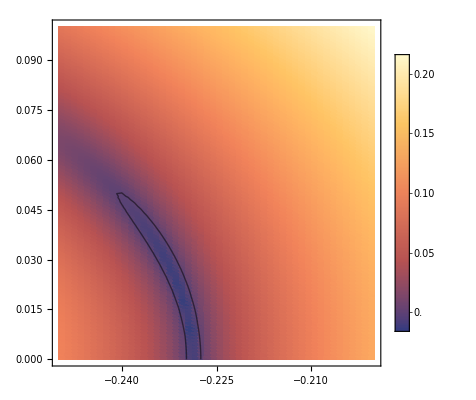

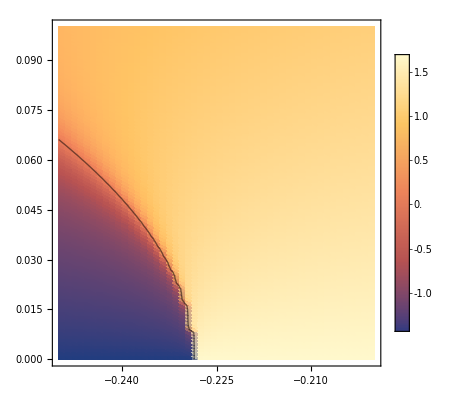

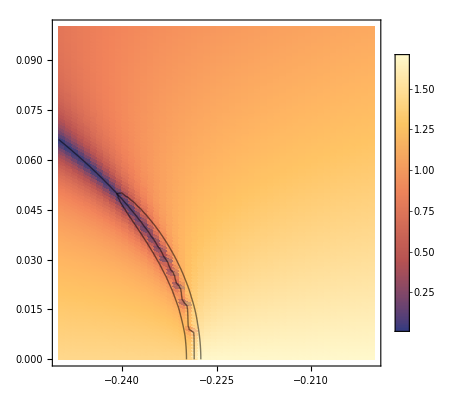

```mathematica
d1=ListDensityPlot[errordata[[All,{1,2,3}]],PlotLegends->Automatic];
d2=ListDensityPlot[errordata[[All,{1,2,4}]],PlotLegends->Automatic];
c1=ListContourPlot[errordata[[All,{1,2,3}]],PlotLegends->Automatic,Contours->{0},ContourShading->None];
c2=ListContourPlot[errordata[[All,{1,2,4}]],PlotLegends->Automatic,Contours->{0},ContourShading->None];
dnorm=ListDensityPlot[errornormdata,PlotLegends->Automatic];
p1=Show[d1,c1]
p2=Show[d2,c2]
pnorm=Show[dnorm,c1,c2]
```

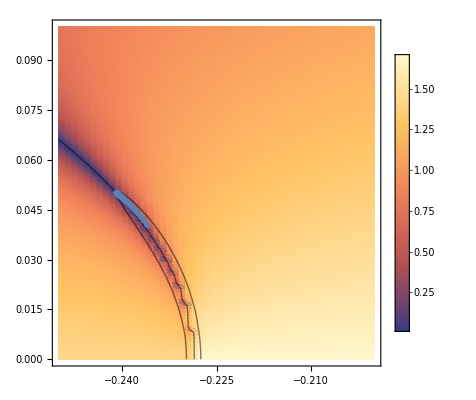

-(0.0215763 km)/s

(0.0424424 km)/s

{-(0.0215763 km)/s,(0.0424424 km)/s}

```mathematica
Show[pnorm,ListPlot[XState[[1;;50]]]]
```

```mathematica
Norm[{deltavxkms, deltavykms}]
```

0.0476119 Abs[km/s]

```mathematica
amm/day/.amm-> 384400km/.day-> 86400 s
```

(961 km)/(216 s)